## Figure 1

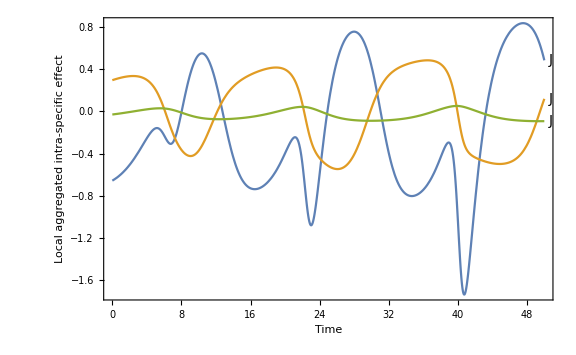
| 
-Graphics-A | -Graphics-B

```mathematica
(*Hastings's chaotic food-web model and chosen model parameters DOI: 10.2307/1940591*)
a1=5;b1=4;a2=.5;b2=2;d1=.4;d2=.1;timelength=50;
eqns = {
x[t](1-x[t])-y[t]a1 x[t]/(1+b1 x[t]),
y[t]a1 x[t]/(1+b1 x[t]) - z[t]a2 y[t]/(1+b2 y[t])-d1 y[t], 
z[t]a2 y[t]/(1+b2 y[t]) - d2 z[t]
};
(*Solve the ODEs with the initial conditions*)
solution = NDSolve[{
x'[t]==eqns [[1]],
y'[t]==eqns [[2]], 
z'[t]==eqns [[3]],
x[0]==.8,y[0]==.2,z[0]==1},{x,y,z},{t,0,timelength}];
(*Get the analytic Jacobian elements*)
jacobian =D[eqns,{{x[t],y[t],z[t]}}];
(*Plot the legends*)
legend=LineLegend[
{Directive[RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]]},
{"d SubscriptBox[N, 1]","d SubscriptBox[N, 2]","d SubscriptBox[N, 3]"},
LegendLayout->{"Row",1},
LabelStyle->15,
LegendLabel->Style["Parametric pairwise formalism",18]
];
(*Plot Panel A*)
network=Graph[{1->2,2->3,1->1},PlotTheme->"Monochrome",
VertexStyle->{1 -> RGBColor[0.368417, 0.506779, 0.709798], 2 ->RGBColor[0.880722, 0.611041, 0.142051], 3->RGBColor[0.560181, 0.691569, 0.194885]}, VertexSize->.3,VertexCoordinates->{{0.,0},{0.,.5},{0.,1}},
ImageSize->{70,350},
VertexLabels->{1->Placed[Style[1,FontSize->15],After],2->Placed[Style[2,FontSize->15],After],3->Placed[Style[3,FontSize->15],After]}
];
(*Plot Panel B*)
intra=Plot[Evaluate[Diagonal[jacobian]/.solution ], {t,0,timelength},
ImageSize->Large,PlotRange->All,
PlotLabels->Placed[{Style["J",FontSize->14],Style["J",FontSize->14],Style["J",FontSize->14]},After],
Frame->True,
FrameLabel->{Style["Time",FontSize->20],Style["Local aggregated \n intra-specific effect",FontSize->20]}];
(*Combine Panels A and B*)
AddLabel[x_,label_]:=Labeled[x,Style[label,FontSize->18],{{Left,Top}}];
Grid[{{legend,SpanFromLeft},{AddLabel[network,"A"],AddLabel[intra,"B"]}},Spacings->{2,2},Frame->None]
```

## Figure 2

#### competition population dynamics without higher-order direct effects

```mathematica
(*governing population dynamics without higher-order direct effects*)
eqns={
x[t](2.6-x[t]-1.5y[t]-.1z[t]),
y[t](1.7-.1x[t]-y[t]-.6z[t]), 
z[t](3.1-1.6x[t]-.5y[t]-z[t])
};
(*solve the ODEs with given initials*)
timelength=6;
solution = NDSolve[{
x'[t]==eqns[[1]],
y'[t]==eqns[[2]], 
z'[t]==eqns[[3]],
x[0]==1,y[0]==.1,z[0]==20},{x,y,z},{t,0,timelength}];
(*get the analytic form of Jacobian*)
jacobian =D[eqns,{{x[t],y[t],z[t]}}];
(*Plot the legend*)
withoutlegend=LineLegend[
{Directive[RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]]},
{"d SubscriptBox[N, 1]N_1-1.5N_2-.1N_3+2.6)","d SubscriptBox[N, 2]","d SubscriptBox[N, 3]"},
LegendLayout->{"Row",1},
LabelStyle->13,
LegendLabel->Style["Parametric pairwise formalism",18]
];
(*Panel A: time series of species abundance*)
withouttime=LogPlot[Evaluate[{x[t],y[t],z[t]}/.solution ], {t,0,timelength},
ImageSize->Medium,
PlotLabels->Placed[{Style["N",FontSize->14],Style["N",FontSize->14],Style["N",FontSize->14]},Above],
Frame->True,FrameLabel->{Style["Time",FontSize->14],Style["Species abundance",FontSize->14]}
];
(*Panel B: time series of Jacobian elements*)
withoutinter=Plot[Evaluate[{jacobian[[1,2]],jacobian[[1,3]]}/.solution ], {t,0,timelength},
ImageSize->Medium,PlotRange->{-4,3},
PlotTheme->"Monochrome",PlotLabels->Placed[{Style["J_12=-1.5N_1",FontSize->14],Style["J_13=-.1N_1",FontSize->14]},Below],
Frame->True,FrameLabel->{Style["Time",FontSize->14],Style["Local aggregated \n interspecific effect",FontSize->14]}
];
(*jacobian[[1,3]]*)
```

#### competition population dynamics with higher-order direct effects

```mathematica
(*governing population dynamics with higher-order direct effects*)
eqns={
x[t](2.6-x[t]-1.5y[t]-.1z[t]+y[t]z[t]),
y[t](1.7-.1x[t]-y[t]-.6z[t]), 
z[t](3.1-1.6x[t]-.5y[t]-z[t])
};
(*solve the ODEs with given initials*)
solution = NDSolve[{
x'[t]==eqns[[1]],
y'[t]==eqns[[2]], 
z'[t]==eqns[[3]],
x[0]==1,y[0]==.1,z[0]==20},{x,y,z},{t,0,timelength}];
(*get the analytic form of Jacobian*)
jacobian =D[eqns,{{x[t],y[t],z[t]}}];
(*Plot the legend*)
withlegend=LineLegend[
{Directive[RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]]},
{Row[{"d SubscriptBox[N, 1]N_1-1.5N_2-.1N_3+2.6",Style["+N_2N_3",Red,Bold],")"}],"d SubscriptBox[N, 2]","d SubscriptBox[N, 3]"},
LegendLayout->{"Row",1},
LabelStyle->13,
LegendLabel->Style["Parametric higher-order formalism",18]
];
(*Panel C: time series of species abundance*)
withtime=LogPlot[Evaluate[{x[t],y[t],z[t]}/.solution ], {t,0,timelength},
(*PlotLabel->Style["Abundance timeseries",FontSize->18],*)
ImageSize->Medium,
PlotLabels->Placed[{Style["N",FontSize->14],Style["N",FontSize->14],Style["N",FontSize->14]},Above],
Frame->True,FrameLabel->{Style["Time",FontSize->14],Style["Species abundance",FontSize->14]}
];
(*Panel D: time series of Jacobian elements*)
withinter=Plot[Evaluate[{jacobian[[1,2]],jacobian[[1,3]]}/.solution ], {t,0,timelength},
ImageSize->Medium,PlotRange->{-4,3},
PlotTheme->"Monochrome",PlotLabels->Placed[{Style["J_12 = N_1(-1.5+N_3)",FontSize->14],Style["J_13=N_1(-.1+N_2)",FontSize->14]},{{3,-2.3},Above}],
Frame->True,FrameLabel->{Style["Time",FontSize->14],Style["Local aggregated \n interspecific effect",FontSize->14]}
];
(*jacobian[[1,3]]*)
```

#### Plot Figure 2

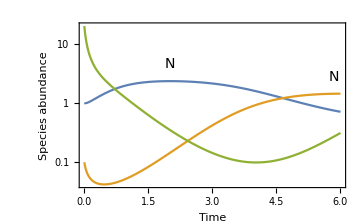
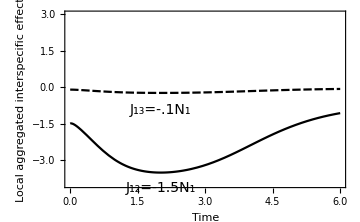
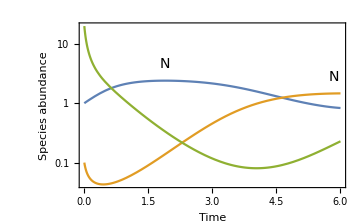
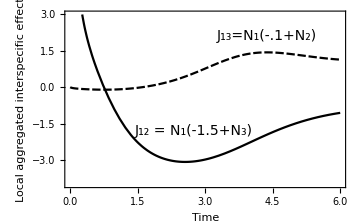
| 
-Graphics-(A) | -Graphics-(B)
 | 
-Graphics-(C) | -Graphics-(D)

/Users/chuliangsong/Dropbox (Personal)/MIT Research/define_interaction/inter.pdf

```mathematica
(*Combine Panels A-D*)
AddLabel[x_,label_]:=Labeled[x,Style[label,FontSize->18],{{Left,Top}}];
Grid[
{{Grid[{
{withoutlegend,SpanFromLeft},
{AddLabel[withouttime,"(A)"],AddLabel[withoutinter,"(B)"]}},
Spacings->{2,2},Frame->None,Alignment->Center]},
{Grid[{
{withlegend,SpanFromLeft},
{ AddLabel[withtime,"(C)"],AddLabel[withinter,"(D)"]}},
Spacings->{2,2},Frame->None,Alignment->Center]}},
Spacings->{2,2},
Dividers->{{False,False,False},{2->{Gray,Dotted,Thick}}}]
Export["/Users/chuliangsong/Dropbox (Personal)/MIT Research/define_interaction/inter.pdf",%]
```

```mathematica
Row[{"d SubscriptBox[N, 1]N_1",Framed["-1.5"],"N_2",Framed["-.1",FrameStyle->Directive[Dashed]],"N_3+2.6",Style["+N_2N_3",Red,Bold],")"}]
```